If there η1 = η2   then there is an extra 1/2 which comes from the Cos[η (t])^2 term.   This term is really Y1 Y2 and is Sin[] Sin[] so we need to be more careful than what I have done here.

## Averaging over η t

```mathematica
Hη[ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_]:=Block[{htp, h1,h2,h3,h12,h23,h31,h123, Ω1,ωr1,ϕ1, Ω2,ωr2,ϕ2, Ω3,ωr3,ϕ3,ω1,ω2,ω3,ω12,ω23,ω31,ζ1,ζ2,ζ3,η1,η2,η3},
Ω1=Ωl[[1]];  ωr1 = ωrl[[1]];  ϕ1 = ϕl[[1]];
Ω2=Ωl[[2]];    ωr2 = ωrl[[2]];  ϕ2 = ϕl[[2]];
Ω3=Ωl[[3]];    ωr3 = ωrl[[3]];  ϕ3 = ϕl[[3]];
ω1 = ωl[[1]];  ω2 = ωl[[2]];  ω3 = ωl[[3]];
ω12 = ω2l[[1]]; ω23 = ω2l[[2]]; ω31 = ω2l[[3]];
ζ1=ArcTan[(ω1-ωr1)/Ω1];    ζ2=ArcTan[(ω2-ωr2)/Ω2];    ζ3=ArcTan[(ω3-ωr3)/Ω3];  
η1=√((ω1-ωr1)^2+Ω1^2);  η2=√((ω2-ωr2)^2+Ω2^2); η3=√((ω3-ωr3)^2+Ω3^2);


h12=3/8 ω12( Cos[t ωr1+ϕ1+t ωr2+ϕ2]+Cos[t ωr1+ϕ1-t ωr2-ϕ2])Cos[ζ2] Cos[ζ1] ( X1.X2  );
h23=3/8 ω23( Cos[t ωr2+ϕ2+t ωr3+ϕ3]+Cos[t ωr2+ϕ2-t ωr3-ϕ3])Cos[ζ3] Cos[ζ2] ( X2.X3  );
h31=3/8 ω31( Cos[t ωr3+ϕ3+t ωr1+ϕ1]+Cos[t ωr3+ϕ3-t ωr1-ϕ1])Cos[ζ1] Cos[ζ3] ( X3.X1  );

h123=3/8 Λ( Cos[t ωr1+ϕ1+t ωr2+ϕ2+t ωr3+ϕ3]+Cos[t ωr1+ϕ1+t ωr2+ϕ2-t ωr3-ϕ3]+Cos[t ωr1+ϕ1-t ωr2-ϕ2+t ωr3+ϕ3]+Cos[t ωr1+ϕ1-t ωr2-ϕ2-t ωr3-ϕ3])Cos[ζ2] Cos[ζ1]Cos[ζ3] (X3. X1.X2  );

htp =h12+h23+h31+h123;

htp
];
```

```mathematica
Uη[ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_,dt_]:=Block[{utp,ti,ut,ht,et,ψt},
utp=I0[3];
ht=Hη[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t];
{et,ψt}=Eigensystem[ht];
utp =Transpose[ψt].DiagonalMatrix[ⅇ^(-ⅈ et dt)].Conjugate[ψt];

utp
];
```

```mathematica
ωl={0.5,0.51,0.49};
ω2l={0.03,0.04,0.02};
Ωl={0.4,0.4,0.00001};
ωrl={0.4,0.4,0.4};
ϕl={0.5,0.5,0.5};
t=0.5;
Λ=0.01*0;
```

```mathematica
dt=0.2;
t=200;
z1l={};
z2l={};
z3l={};
za1l={};
za2l={};
za3l={};
zc1l={};
zc2l={};
zc3l={};
zη1l = {};
zη2l={};
zη3l={};
ψt=X1.ψ000;
ψt=Rc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,0].ψt;
ψat=X1.ψ000;
ψat=Rc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,0].ψat;
ψct=X1.ψ000;
ψct=ψct;
ψηt=X1.ψ000;
For[ti=dt,ti≤t,ti+=dt,
ψt=Uaeff[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt].ψt;
ψot=Conjugate[Transpose[Rc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti]]].ψt;

z1=Conjugate[ψot].Z1.ψot;
z2=Conjugate[ψot].Z2.ψot;
z3=Conjugate[ψot].Z3.ψot;

z1l=Join[z1l,{{ti,z1}}];
z2l=Join[z2l,{{ti,z2}}];
z3l=Join[z3l,{{ti,z3}}];



ψat=Ua[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt].ψat;
ψaot=Conjugate[Transpose[Rc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti]]].ψat;

za1=Conjugate[ψaot].Z1.ψaot;
za2=Conjugate[ψaot].Z2.ψaot;
za3=Conjugate[ψaot].Z3.ψaot;

za1l=Join[za1l,{{ti,za1}}];
za2l=Join[za2l,{{ti,za2}}];
za3l=Join[za3l,{{ti,za3}}];


ψct=Uc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt].ψct;
ψcot=ψct;

zc1=Conjugate[ψcot].Z1.ψcot;
zc2=Conjugate[ψcot].Z2.ψcot;
zc3=Conjugate[ψcot].Z3.ψcot;

zc1l=Join[zc1l,{{ti,zc1}}];
zc2l=Join[zc2l,{{ti,zc2}}];
zc3l=Join[zc3l,{{ti,zc3}}];


ψηt=Uη[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt].ψηt;
zη1=Conjugate[ψηt].Z1.ψηt;
zη2=Conjugate[ψηt].Z2.ψηt;
zη3=Conjugate[ψηt].Z3.ψηt;

zη1l=Join[zη1l,{{ti,zη1}}];
zη2l=Join[zη2l,{{ti,zη2}}];
zη3l=Join[zη3l,{{ti,zη3}}];

];
```

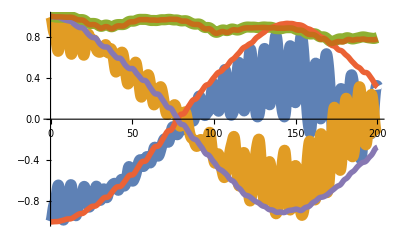

```mathematica
ListPlot[{za1l,za2l,za3l,z1l,z2l,z3l},Joined->True,PlotStyle->{Thickness[0.02],Thickness[0.02],Thickness[0.02],Thickness[0.01],Thickness[0.01],Thickness[0.01]}]
```

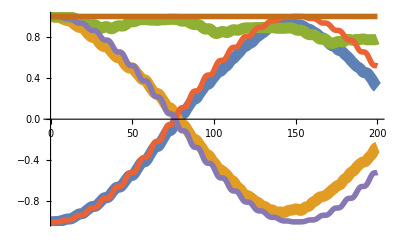

```mathematica
ListPlot[{zc1l,zc2l,zc3l,zη1l,zη2l,zη3l},Joined->True,PlotStyle->{Thickness[0.02],Thickness[0.02],Thickness[0.02],Thickness[0.01],Thickness[0.01],Thickness[0.01]}]
```

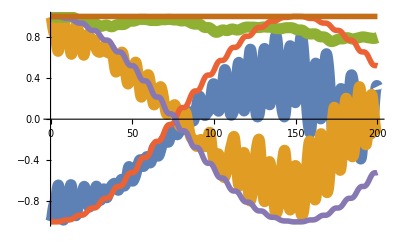

```mathematica
ListPlot[{za1l,za2l,za3l,zη1l,zη2l,zη3l},Joined->True,PlotStyle->{Thickness[0.02],Thickness[0.02],Thickness[0.02],Thickness[0.01],Thickness[0.01],Thickness[0.01]}]
```

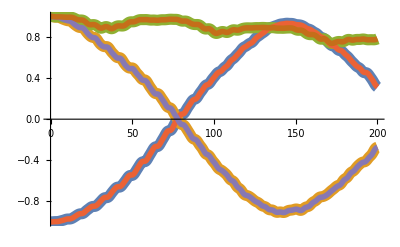

```mathematica
ListPlot[{zc1l,zc2l,zc3l,z1l,z2l,z3l},Joined->True,PlotStyle->{Thickness[0.02],Thickness[0.02],Thickness[0.02],Thickness[0.01],Thickness[0.01],Thickness[0.01]}]
```